```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
```

```mathematica
V[1,2,x_]:=6264.458084510956 x^2
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,2,x]*u[x],{i,1,1}];
```

```mathematica
B=1;H=2000;Neigenvalues=100;
eigensysC=NDEigensystem[ℒallc,u[x],{x,-B*10,B*10},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
Length@eigensysC[[1]]
```

100

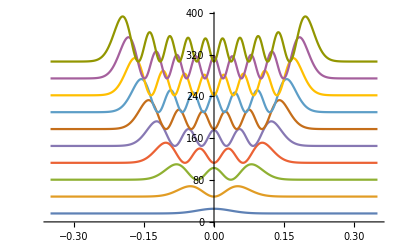

```mathematica
(*Make a nice plot - note eigenvectors are normalised but but eigenvalues aren't necessary close to 1*)
(*Plot Psi*Psi*E_i*0.1 + E_i for first ten eigenvalues and vectors*)
Plot[Evaluate@Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*0.05*eigensysC[[1]][[i]]+eigensysC[[1]][[i]],{i,1,10}],{x,-0.35,0.35}]
```

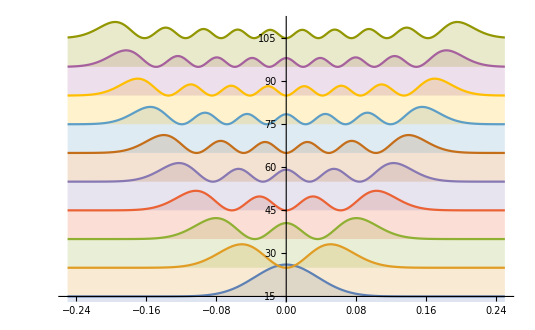

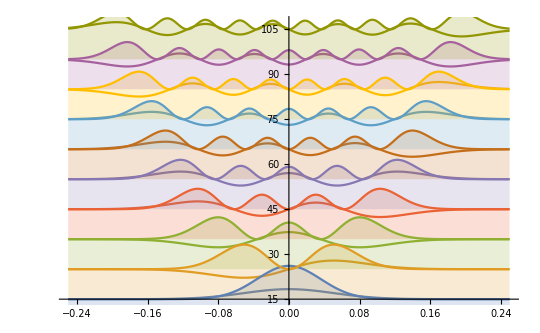

```mathematica
(*Plot Psi*Psi + 0.4*E_i for first ten eigenvalues and vectors*)
Plot[Evaluate[Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]+10i+5,{i,1,10}],{x,-0.25,0.25}],Filling->Table[i->(10i-5),{i,1,10}]]
(*Plot Psi*Psi + 0.4*E_i for first ten eigenvalues and vectors*)
Show[Plot[Evaluate[Table[eigensysC[[2]][[i]]+10i+5,{i,1,10}],{x,-0.25,0.25}]],Plot[Evaluate[Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]+10i+5,{i,1,10}],{x,-0.25,0.25}],Filling->Table[i->(10i-5),{i,1,10}]]]
```

```mathematica
V[1,2,x]
```

6264.46 x^2

```mathematica
eigensysC[[1]][[1]]
```

16.1489

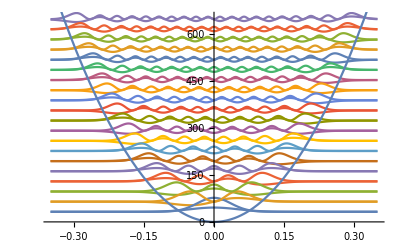

```mathematica
(*Plot Psi*Psi + 0.4*E_i for first ten eigenvalues and vectors*)
Show[Plot[Evaluate[Table[eigensysC[[2]][[i]]*4+4eigensysC[[1]][[1]]*i(1-0.5),{i,1,20}],{x,-0.35,0.35}]],Plot[Evaluate[Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*4+4eigensysC[[1]][[1]]*i(1-0.5),{i,1,20}]],{x,-0.35,0.35}],Plot[Evaluate@V[1,2,x],{x,-0.35,0.35}]]
```

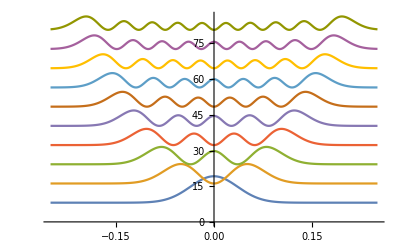

```mathematica
Plot[Evaluate[Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]+eigensysC[[1]][[1]]*i(1-0.5),{i,1,10}]],{x,-0.25,0.25}]
```

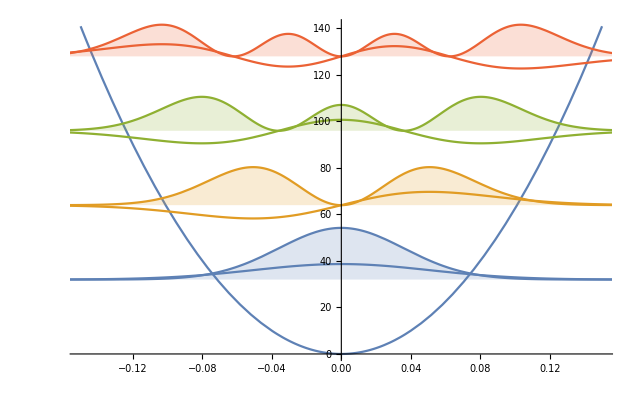

```mathematica
(*Plot Psi*Psi + 0.4*E_i for first ten eigenvalues and vectors*)
Show[Plot[Evaluate@V[1,2,x],{x,-0.15,0.15}],Plot[Evaluate[Table[eigensysC[[2]][[i]]*2+64i(1-0.5),{i,1,10}],{x,-0.25,0.25}]],Plot[Evaluate[Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*2+64i(1-0.5),{i,1,10}],{x,-0.25,0.25}],Filling->Table[i->(64i(1-0.5)),{i,1,10}]]]
```

```mathematica
(*Chemical potential with arguments in meV*)
(*Why are energies randomly multiplied by four??*)
n[omega_,T_,mu_]:=1/(Exp[(4omega-kB*mu)/(kB*T)]-1)
```

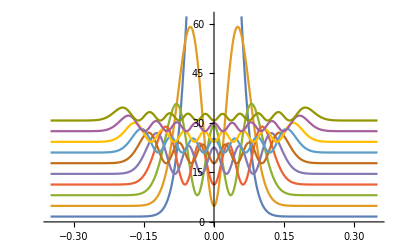

```mathematica
(* Plot Psi*Psi*n(Ei,T,mu) + 0.1*Ei *)
Plot[Evaluate@Table[n[eigensysC[[1]][[i]],4000](eigensysC[[2]][[i]]*eigensysC[[2]][[i]])+0.1eigensysC[[1]][[i]],{i,1,10}],{x,-0.35,0.35}]
```

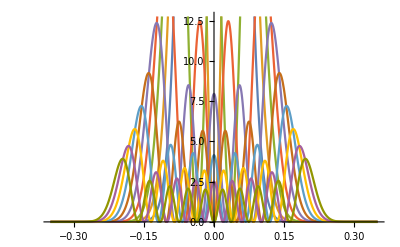

```mathematica
(*Temperature scaled eigenmodes for einstein oscailltor*)
(* Plot Psi*Psi*n(Ei,T,mu) *)Plot[Evaluate@Table[n[eigensysC[[1]][[i]],4000](eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,10}],{x,-0.35,0.35}]
```

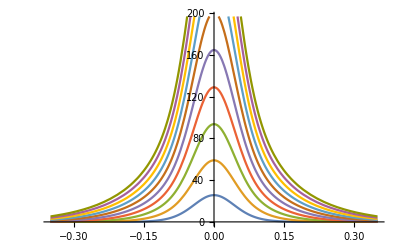

```mathematica
(*Spatial Occupation distrubtion function at different temperatures *)
Plot[Evaluate@Table[Total@Table[n[eigensysC[[1]][[i]],500j](eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,50}],{j,1,10}],{x,-0.35,0.35}]
```

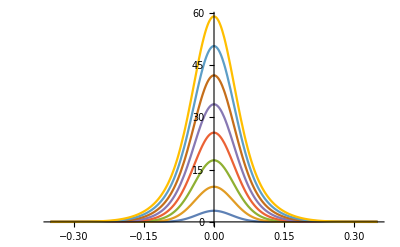

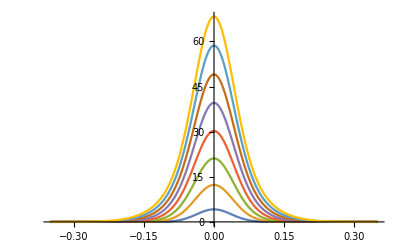

```mathematica
(*Sum[Psi(r)*Psi(r)*n(omega,mu,T)] at T=0,...4000K, for mu=0, for 50 eigenvalues for carbon frequencies*)
Plot[Evaluate@Table[Total@Table[n[eigensysC[[1]][[i]],500j,0](eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,40}],{j,1,8}],{x,-0.35,0.35},PlotRange->All]

(*Sum[Psi(r)*Psi(r)*n(omega,mu,T)] at T=0,...4000K, for mu=100, for 50 eigenvalues for carbon frequencies*)
Plot[Evaluate@Table[Total@Table[n[eigensysC[[1]][[i]],500j,100](eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,40}],{j,1,8}],{x,-0.35,0.35},PlotRange->All]
```

```mathematica
npsipsi=Table[Total@Table[n[eigensysC[[1]][[i]],500j,0](eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,40}],{j,1,8}];
```

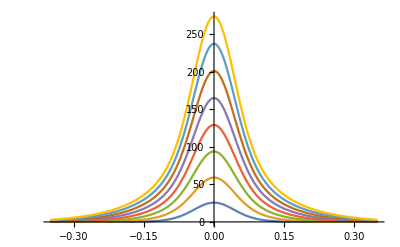

```mathematica
(*Sum[Psi(r)*Psi(r)*n(omega,mu,T)] at T=0,...4000K, for mu=100, for 50 eigenvalues for carbon frequencies*)
Plot[Evaluate@npsipsi,{x,-0.35,0.35},PlotRange->All]
```

```mathematica
pdata=n[eigensysC[[1]][[1]],500,0]*eigensysC[[2]][[1]]*eigensysC[[2]][[1]]
```

2.19925 (InterpolatingFunction[{{-10., 10.}}, <>][x])^2

```mathematica
n[eigensysC[[1]][[1]],4000]
```

20.8486

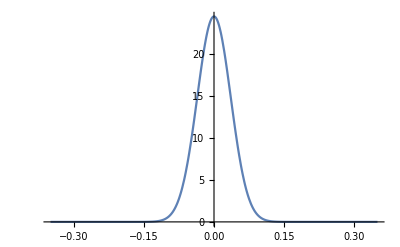

```mathematica
Plot[pdata,{x,-0.35,0.35},PlotRange->All]
```

```mathematica
Integrate[n[eigensysC[[1]][[1]],500,0]*eigensysC[[2]][[1]]*eigensysC[[2]][[1]],{x,-0.35,0.35}]//N
Integrate[n[eigensysC[[1]][[1]],4000,0]*eigensysC[[2]][[1]]*eigensysC[[2]][[1]],{x,-0.35,0.35}]//N
```

2.19925

20.8486

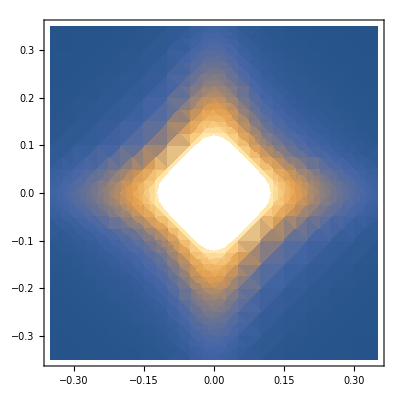

```mathematica
plot=Evaluate@Table[Total@Table[n[eigensysC[[1]][[i]],500j](eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,50}],{j,10,10}];
DensityPlot[(plot/.x->z)*(plot/.x->y),{z,-0.35,0.35},{y,-0.35,0.35}]
```

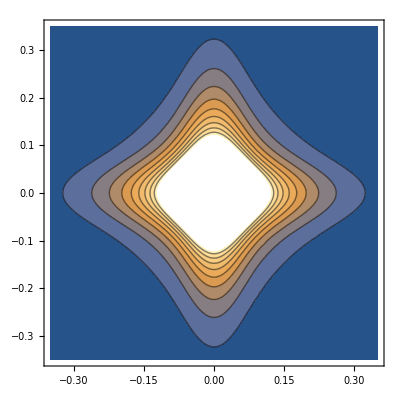

```mathematica
ContourPlot[(plot/.x->z)*(plot/.x->y),{z,-0.35,0.35},{y,-0.35,0.35}]
```

```mathematica
ContourPlot[(plot/.x->z)*(plot/.x->y)+(plot/.x->z)*(plot/.x->y),{z,-0.35,0.35},{y,-0.35,0.35}]
```

-Graphics-

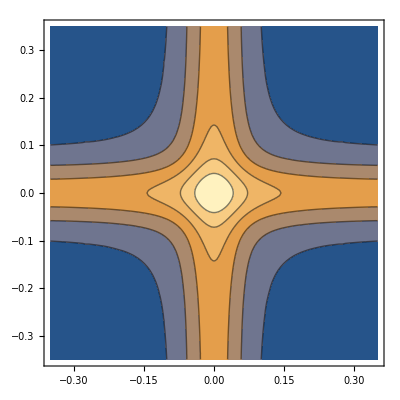

```mathematica
ContourPlot[(plot/.x->z)+(plot/.x->y),{z,-0.35,0.35},{y,-0.35,0.35}]
```

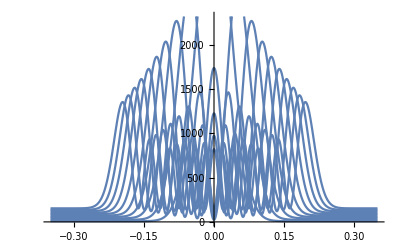

```mathematica
Plot[Evaluate@Table[n[eigensysC[[1]][[i]],T](eigensysC[[2]][[i]]*eigensysC[[2]][[i]])eigensysC[[1]][[i]]+0.5eigensysC[[1]][[i]],{i,1,10}]/.T->4000,{x,-0.35,0.35}]
```

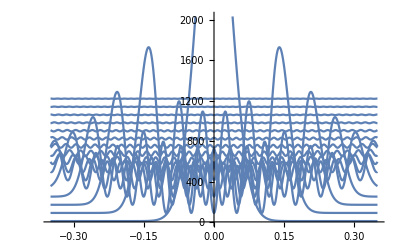

```mathematica
Plot[Evaluate@Table[n[eigensysC[[1]][[i]],T](eigensysC[[2]][[i]]*eigensysC[[2]][[i]])eigensysC[[1]][[i]]+0.5eigensysC[[1]][[i]],{i,1,80,5}]/.T->4000,{x,-0.35,0.35}]
```

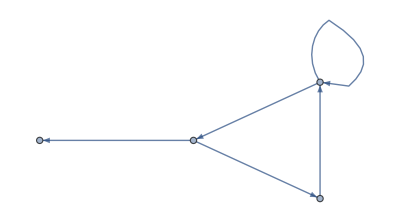

```mathematica
Graph[{1->3,1->2,2->5,5->5,5->1}]
```

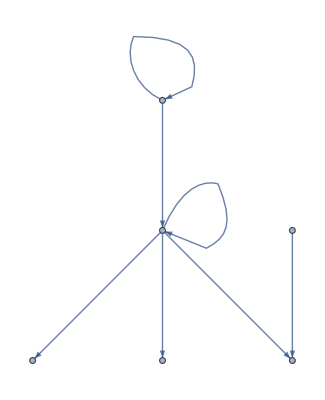

```mathematica
Graph[{1->1,2->2,1->3,1->4,1->5,6->4,2->1}]
```

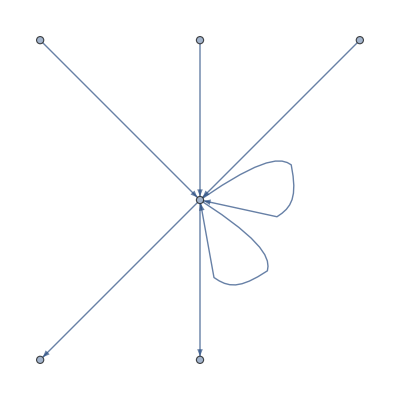

```mathematica
Graph[{1->4,2->4,3->4,4->4,4->4,4->5,4->6}]
```

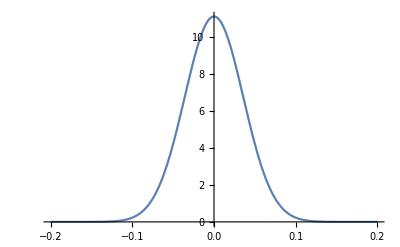

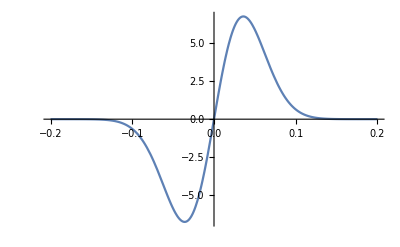

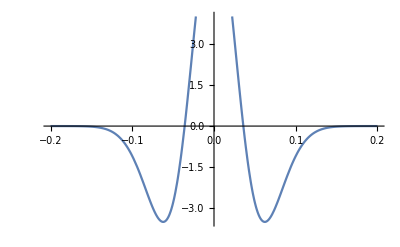

```mathematica
Plot[Table[(eigensysC[[2]][[i]]*eigensysC[[2]][[i]]),{i,1,1}],{x,-0.2,0.2}]
Plot[Table[(eigensysC[[2]][[i]]*eigensysC[[2]][[i+1]]),{i,1,1}],{x,-0.2,0.2}]
Plot[Table[(eigensysC[[2]][[i]]*eigensysC[[2]][[i+2]]),{i,1,1}],{x,-0.2,0.2}]
```

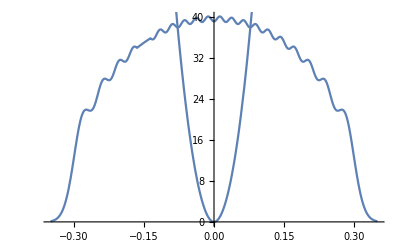

```mathematica
(*Plot Psi*Psi + 0.4*E_i for first ten eigenvalues and vectors*)
Show[Plot[Evaluate[Total@Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]],{i,1,20}]],{x,-0.35,0.35}],Plot[Evaluate@V[1,2,x],{x,-0.35,0.35}]]
```

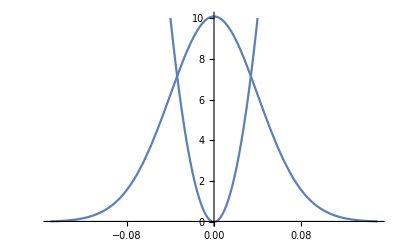

```mathematica
(*Plot Psi*Psi + 0.4*E_i for first ten eigenvalues and vectors*)
Show[Plot[Evaluate[Total@Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*n[eigensysC[[1]][[i]],1000,0],{i,1,20}]],{x,-0.15,0.15},PlotRange->All],Plot[Evaluate@V[1,2,x],{x,-0.04,0.04}]]
```

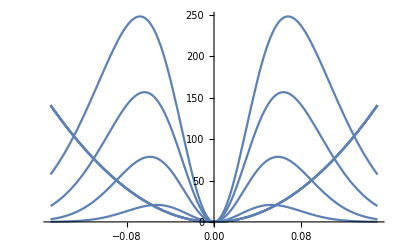

```mathematica
(*Unormalised probability density - Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Show[Plot[Table[{Evaluate@V[1,2,x],Evaluate[Total@Table[Evaluate@V[1,2,x]*eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*n[eigensysC[[1]][[i]],500j,0],{i,1,20}]]},{j,1,4}],{x,-0.15,0.15},PlotRange->All]]
```

```mathematica
e[j_]:=Total@Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*n[eigensysC[[1]][[i]],500j,0],{i,1,20}]
f[j_]:=Total@Table[Evaluate@V[1,2,x]*eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*n[eigensysC[[1]][[i]],500j,0],{i,1,20}]
g=Table[Integrate[Total@Table[Evaluate@V[1,2,x]*eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*n[eigensysC[[1]][[i]],500j,0],{i,1,20}],{x,-1,1}],{j,1,10}]//N
```

{2.61839,11.4823,26.2558,46.9384,73.5272,106.,144.284,188.224,237.573,292.012}

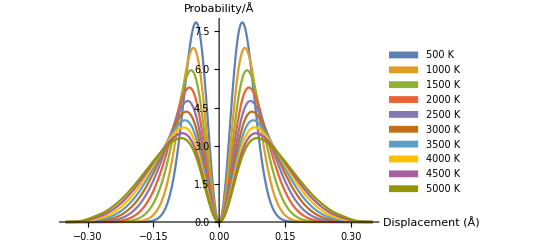

```mathematica
(*Normalised probability density - (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[f[j]/(g[[j]]),{j,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " j*500,{j,1,10}]],AxesLabel->{"Displacement\n(Å)","Probability/Å"}]
```

```mathematica
h=Table[Integrate[Total@Table[eigensysC[[2]][[i]]*eigensysC[[2]][[i]]*n[eigensysC[[1]][[i]],500j,0],{i,1,20}],{x,-1,1}],{j,1,10}]//N
```

{0.299358,1.04485,1.96857,3.00651,4.12906,5.31886,6.56434,7.85701,9.1902,10.5585}

```mathematica
(*Normalised probability density - (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[e[j]/(g[[j]]),{j,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " j*500,{j,1,10}]],AxesLabel->{"Displacement\n(Å)","Probability/Å"}]
```

Interrupted

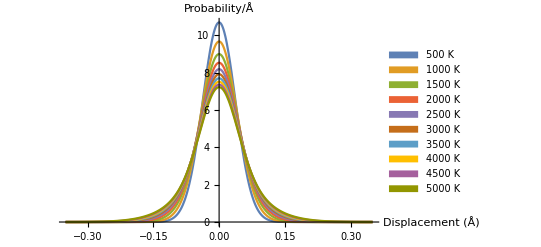

```mathematica
(*Normalised probability density - (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[e[j]/(h[[j]]),{j,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " j*500,{j,1,10}]],AxesLabel->{"Displacement\n(Å)","Probability/Å"}]
```

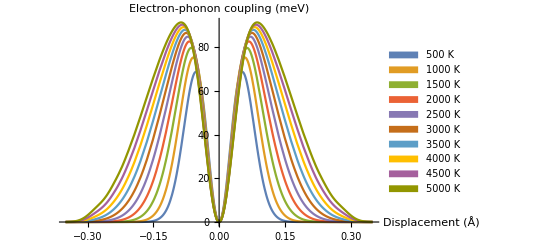

```mathematica
(*Normalised probability density - (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[(e[j]/(h[[j]])*Evaluate@V[1,2,x]),{j,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " j*500,{j,1,10}]],AxesLabel->{"Displacement\n(Å)","Electron-phonon\ncoupling (meV)"}]
```

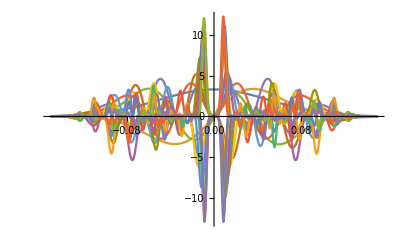

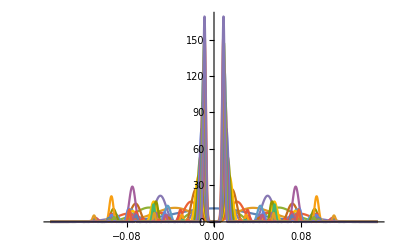

```mathematica
har[j_]:=Product[eigensysC[[2]][[i]],{i,1,j}]
hartree=Table[(har[j])/(Evaluate[Sqrt@Integrate[har[j]*har[j],{x,-0.25,0.25}]//N]),{j,1,20}];
Plot[hartree,{x,-0.15,0.15},PlotRange->All]
Plot[Evaluate@(hartree^2),{x,-0.15,0.15},PlotRange->All]
```

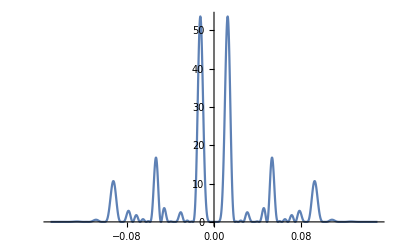

```mathematica
Plot[Evaluate@(hartree^2)[[10]],{x,-0.15,0.15},PlotRange->All]
```

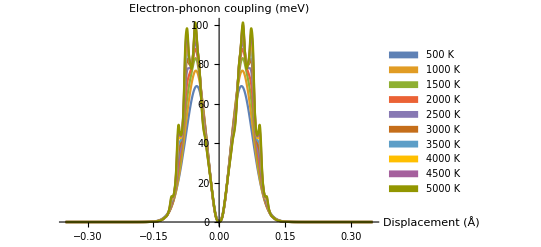

```mathematica
(*Normalised probability density - (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[(g1[k]/(g2[k])*Evaluate@V[1,2,x]),{k,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " k*500,{k,1,10}]],AxesLabel->{"Displacement\n(Å)","Electron-phonon\ncoupling (meV)"}]
```

```mathematica
hartree=Table[(har[j])/(Evaluate[Sqrt@Integrate[har[j]*har[j],{x,-0.25,0.25}]//N]),{j,1,40}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0117265}. NIntegrate obtained 36.2831 and 0.0000566583 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.011711}. NIntegrate obtained 18.7103 and 0.0000350455 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0117265}. NIntegrate obtained 27.5512 and 0.0000357795 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Length[hartree]
(*hartree is the set of normalised hartree product wavefunctions from single product to a product of 20*)
(*g1 is normalised a probability a sum over all combination of hartee products*)
(*g2 the integral of g1 used for normalisation*)
(*g_alt only use a single hatree product of 20 states, not a sum of them...*)

g1[k_]:=Total@Table[hartree[[i]]*hartree[[i]]*n[eigensysC[[1]][[i]],500k,0],{i,1,Length[hartree]}]
g2[k_]:=Integrate[Total@Table[hartree[[i]]*hartree[[i]]*n[eigensysC[[1]][[i]],500k,0],{i,1,Length[hartree]}],{x,-1,1}]//N

g1alt[k_]:=Total@Table[hartree[[i]]*hartree[[i]]*n[eigensysC[[1]][[i]],500k,0],{i,Length[hartree],Length[hartree]}]
g2alt[k_]:=Integrate[Total@Table[hartree[[i]]*hartree[[i]]*n[eigensysC[[1]][[i]],500k,0],{i,Length[hartree],Length[hartree]}],{x,-1,1}]//N
```

40

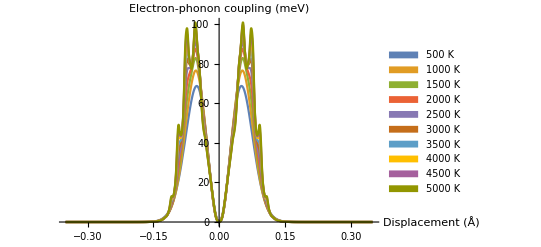

```mathematica
(*Normalised probability density - sum of hartree products- (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[(g1[k]/(g2[k])*Evaluate@V[1,2,x]),{k,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " k*500,{k,1,10}]],AxesLabel->{"Displacement\n(Å)","Electron-phonon\ncoupling (meV)"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00393733}. NIntegrate obtained 1.83019×10^-52 and 1.02357×10^-54 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00393733}. NIntegrate obtained 9.56624×10^-27 and 5.35013×10^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.00393733}. NIntegrate obtained 3.57676×10^-18 and 2.00038×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

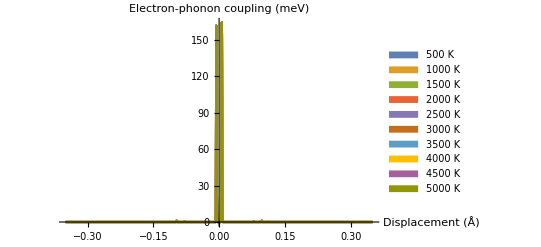

```mathematica
(*Normalised probability density - 20 state hartree product- (1/(Psi*Psi*n))*Sum[Psi(r)*Psi(r)*n(omega,T)*V(r)]*)
Plot[Evaluate@Table[(g1alt[k]/(g2alt[k])*Evaluate@V[1,2,x]),{k,1,10}],{x,-0.35,0.35},PlotRange->All,PlotLegends->SwatchLegend[Table["K " k*500,{k,1,10}]],AxesLabel->{"Displacement\n(Å)","Electron-phonon\ncoupling (meV)"}]
```

```mathematica
(*Integrated electron phonon coupling for Hatree product wavefunction - units meVAng*)
elphValuesHartree=Integrate[Evaluate@Table[(g1[k]/(g2[k])*Evaluate@V[1,2,x]),{k,1,10}],{x,-0.35,0.35}]
```

```mathematica
(*Integrated electron phonon coupling for harmonic functions - units meVAng*)
elphValues=Integrate[Evaluate@Table[(e[j]/(h[[j]])*Evaluate@V[1,2,x]),{j,1,10}],{x,-0.35,0.35}]//N;
```

```mathematica
elphValues//TableForm
```

8.74667
10.9895
13.3375
15.6123
17.8073
19.9291
21.9799
23.956
25.8504
27.6563

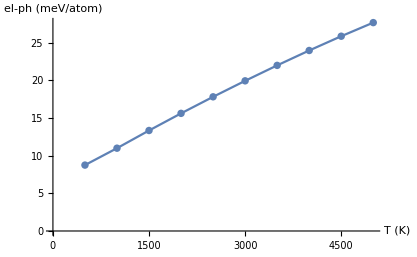

```mathematica
temps=Table[500i,{i,1,10}];
Show[ListPlot[Transpose[{temps,elphValues}],AxesLabel->{"T (K)","el-ph (meV/atom)"}],ListLinePlot@Transpose[{temps,elphValues}]]
```